# SLOVENIJA - GOSPODARSKI IN DEMOGRAFSKI TRENDI

## 1. DEMOGRAFIJA

Najprej začnemo z rodnostjo.

```mathematica
pot = NotebookDirectory[]
```

C:\Users\bogda\OneDrive - Univerza v Ljubljani\Desktop\ROM\Projektna naloga\

Pridobivanje podatkov

```mathematica
umrljivostPod = Import[pot <> "osnovni podatki o umrlih.xlsx", "Dataset", "HeaderLines" -> 1] // First;
```

```mathematica
umrljivostSpolSkupaj = umrljivostPod // Query[;;69];
```

```mathematica
prebivalstvoPod = Import[pot <> "prebivalstvo po starosti.xlsx", "Dataset", "HeaderLines" -> 1] // First;
```

```mathematica
rodnostPod = Import[pot <> "osnovni podatki o rojenih.xlsx", "Dataset", "HeaderLines" -> 1] // First;
```

### 1. Osnovna predstavitev celotne stopnje rodnosti, umrljivosti in prebivalstva

#### Rodnost

```mathematica
rodnostPod[74] // First
```

Živorojen je otrok, ki je takoj po rojstvu pokazal znake življenja (dihanje, srčni utrip, trzanje mišic), čeprav le za krajši čas. Trajanje nosečnosti ni pomembno.
 
Živorojeni na 1000 prebivalcev je razmerje med številom živorojenih otrok v koledarskem letu in številom prebivalstva sredi istega leta, pomnoženo s 1000.
 
Celotna stopnja rodnosti je povprečno število živorojenih otrok na eno žensko v rodni dobi (15-49 let) v koledarskem letu.
 
Bruto stopnja obnavljanja prebivalstva za koledarsko leto pomeni povprečno število živorojenih deklic, ki bi jih rodila generacija žensk v svoji rodni dobi (15-49 let), če bi bile njihove starostnospecifične stopnje rodnosti enake kot v opazovanem letu.
 
Neto stopnja obnavljanja prebivalstva za koledarsko leto pomeni povprečno število živorojenih deklic, ki bi jih rodila generacija žensk v svoji rodni dobi (15-49 let), če bi bile njihove starostnospecifične stopnje rodnosti in umrljivosti enake kot v opazovanem letu.
 
Povprečna starost matere ob rojstvu otroka je tehtana aritmetična sredina starosti mater ob rojstvu otroka.
 
Otrok, rojen zunaj zakonske zveze, je živorojen ali mrtvorojen otrok, ki ga je rodila samska mati, mati, ki živi v zunajzakonski skupnosti, ali mati, ki je bila poročena, pa je od smrti moža oziroma od razveze zakonske zveze do rojstva otroka minilo več kot 300 dni.
 
Mrtvorojeni je otrok, ki je bil rojen brez znakov življenja (ni dihal, ni gibal, srce ni utripalo), in je ob porodu tehtal najmanj 500 gramov, oziroma je nosečnost trajala najmanj 22 tednov ali je bila dolžina njegovega telesa vsaj 25 centimetrov. V primeru, da se pri večplodni nosečnosti (nosečnost z dvojčki, trojčki) eden izmed otrok rodi kot živorojen, štejemo med mrtvorojene tudi njegov mrtvorojeni par, kljub temu, da je lažji od 500 gramov.
 
Mrtvorojeni na 1000 živorojenih je razmerje med številom mrtvorojenih in številom živorojenih otrok v koledarskem letu, pomnoženo s 1000.

```mathematica
rodnostPod = rodnostPod[;;69]
```

Na voljo nam je že stolpec, ki vsebuje stopnjo rodnosti. Najprej si vizualiziramo.

```mathematica
leta = rodnostPod // Query[All, "Leto"] // Normal // ToExpression
```

{1954,1955,1956,1957,1958,1959,1960,1961,1962,1963,1964,1965,1966,1967,1968,1969,1970,1971,1972,1973,1974,1975,1976,1977,1978,1979,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022}

Preverimo da so podatki številčni (ja, s ToExpression)

```mathematica
Head[leta[[1]]]
```

Integer

```mathematica
rodnosti = rodnostPod // Query[All, "Celotna stopnja rodnosti"] // Normal // ToExpression
```

{2.58,2.58,2.51,2.38,2.22,2.23,2.18,2.26,2.27,2.28,2.32,2.45,2.48,2.38,2.28,2.17,2.21,2.16,2.14,2.18,2.1,2.16,2.17,2.16,2.19,2.22,2.11,1.96,1.93,1.82,1.75,1.72,1.65,1.64,1.63,1.52,1.46,1.42,1.34,1.33,1.32,1.29,1.28,1.25,1.23,1.21,1.26,1.21,1.21,1.2,1.25,1.26,1.31,1.38,1.53,1.53,1.57,1.56,1.58,1.55,1.58,1.57,1.58,1.62,1.61,1.61,1.6,1.64,1.55}

```mathematica
podatkiZaIzpis = Transpose[{leta, rodnosti}]
```

{{1954,2.58},{1955,2.58},{1956,2.51},{1957,2.38},{1958,2.22},{1959,2.23},{1960,2.18},{1961,2.26},{1962,2.27},{1963,2.28},{1964,2.32},{1965,2.45},{1966,2.48},{1967,2.38},{1968,2.28},{1969,2.17},{1970,2.21},{1971,2.16},{1972,2.14},{1973,2.18},{1974,2.1},{1975,2.16},{1976,2.17},{1977,2.16},{1978,2.19},{1979,2.22},{1980,2.11},{1981,1.96},{1982,1.93},{1983,1.82},{1984,1.75},{1985,1.72},{1986,1.65},{1987,1.64},{1988,1.63},{1989,1.52},{1990,1.46},{1991,1.42},{1992,1.34},{1993,1.33},{1994,1.32},{1995,1.29},{1996,1.28},{1997,1.25},{1998,1.23},{1999,1.21},{2000,1.26},{2001,1.21},{2002,1.21},{2003,1.2},{2004,1.25},{2005,1.26},{2006,1.31},{2007,1.38},{2008,1.53},{2009,1.53},{2010,1.57},{2011,1.56},{2012,1.58},{2013,1.55},{2014,1.58},{2015,1.57},{2016,1.58},{2017,1.62},{2018,1.61},{2019,1.61},{2020,1.6},{2021,1.64},{2022,1.55}}

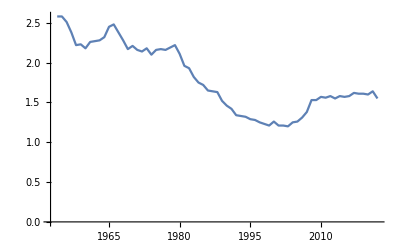

```mathematica
rodnostPlot = ListLinePlot[podatkiZaIzpis]
```

V zadnjih letih je rodnost okoli 1.6. Za stabilno prebivalstvo sta potrebna stopnja 2.1 otroka na žensko. Preverimo še umrljivost, zadnjih let leto, ki naj bi odstopala.

#### Umrljivost

```mathematica
umrljivostSpolSkupaj
```

```mathematica
umrljivostLeta = umrljivostSpolSkupaj // Query[All, "Leto"] // Normal // ToExpression
```

{1954,1955,1956,1957,1958,1959,1960,1961,1962,1963,1964,1965,1966,1967,1968,1969,1970,1971,1972,1973,1974,1975,1976,1977,1978,1979,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022}

```mathematica
umrljivostUmrli = umrljivostSpolSkupaj // Query[All, "Umrli"] // Normal // ToExpression
```

{14897.,15109.,16351.,14545.,14082.,15357.,15145.,14013.,15866.,15102.,16729.,15987.,15248.,16353.,17446.,18565.,17353.,17425.,18153.,17614.,17206.,18180.,18157.,17633.,18357.,18148.,18820.,18733.,19647.,20703.,20214.,19854.,19499.,19837.,19126.,18669.,18555.,19324.,19333.,20012.,19359.,18968.,18620.,18928.,19039.,18885.,18588.,18508.,18701.,19451.,18523.,18825.,18180.,18584.,18308.,18750.,18609.,18699.,19257.,19334.,18886.,19834.,19689.,20509.,20485.,20588.,24016.,23261.,22492.}

```mathematica
umrljivostPodZaIzpis = Transpose[{umrljivostLeta, umrljivostUmrli}]
```

{{1954,14897.},{1955,15109.},{1956,16351.},{1957,14545.},{1958,14082.},{1959,15357.},{1960,15145.},{1961,14013.},{1962,15866.},{1963,15102.},{1964,16729.},{1965,15987.},{1966,15248.},{1967,16353.},{1968,17446.},{1969,18565.},{1970,17353.},{1971,17425.},{1972,18153.},{1973,17614.},{1974,17206.},{1975,18180.},{1976,18157.},{1977,17633.},{1978,18357.},{1979,18148.},{1980,18820.},{1981,18733.},{1982,19647.},{1983,20703.},{1984,20214.},{1985,19854.},{1986,19499.},{1987,19837.},{1988,19126.},{1989,18669.},{1990,18555.},{1991,19324.},{1992,19333.},{1993,20012.},{1994,19359.},{1995,18968.},{1996,18620.},{1997,18928.},{1998,19039.},{1999,18885.},{2000,18588.},{2001,18508.},{2002,18701.},{2003,19451.},{2004,18523.},{2005,18825.},{2006,18180.},{2007,18584.},{2008,18308.},{2009,18750.},{2010,18609.},{2011,18699.},{2012,19257.},{2013,19334.},{2014,18886.},{2015,19834.},{2016,19689.},{2017,20509.},{2018,20485.},{2019,20588.},{2020,24016.},{2021,23261.},{2022,22492.}}

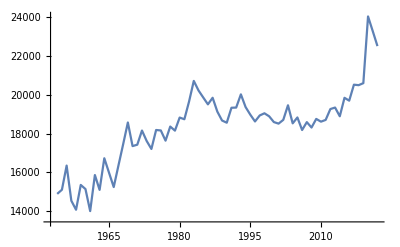

```mathematica
umrljivostPlot = ListLinePlot[umrljivostPodZaIzpis]
```

Število umrlih leta 2020 in 2021 je v eksecu, kot pričakovano zaradi Covid-a. Vendar pa opazimo,  da od leta 1960 umrljivost narašča. Preverimo prebivalstvo.

#### Prebivalstvo

```mathematica
prebivalstvoSkupaj = prebivalstvoPod[;;1, 2;;]
```

```mathematica
prebivalstvoPlot = ListLogPlot[prebivalstvoSkupaj];
```

```mathematica
ListLogPlot[prebivalstvoSkupaj , Frame -> True, FrameTicks -> {{None, All}, {None, None}}]
```

-Graphics-

```mathematica
GraphicsRow[{rodnostPlot, prebivalstvoPlot, umrljivostPlot} ]
```

-Graphics-

### 2. Prebivalstvo po starosti

```mathematica
prebivalstvoPod
```

```mathematica
stPrebivalcev =prebivalstvoPod // Query[2;;86, "2008H1"] // Normal;
starosti = prebivalstvoPod // Query[2;;86, "Polletje"] // Normal;
```

```mathematica
polLeta = (prebivalstvoPod // Keys // First // Normal)[[3;;]]
```

{2010H2,2011H1,2011H2,2012H1,2012H2,2013H1,2013H2,2014H1,2014H2,2015H1,2015H2,2016H1,2016H2,2017H1,2017H2,2018H1,2018H2,2019H1,2019H2,2020H1,2020H2,2021H1,2021H2,2022H1,2022H2,2023H1}

```mathematica
Manipulate[
Table[BarChart[prebivalstvoPod // Query[2;;86, polLetje] // Normal, 
PlotLabel -> polLetje,
ChartLabels -> Placed[starosti, p, Rotate[#, Pi / 2]&], 
ImageSize -> 750], 
{p, {Top}}] // First,
{polLetje, polLeta, ControlType -> Slider}]
```

## 2. GOSPODARSTVO

```mathematica
pot = NotebookDirectory[]
```

C:\Users\bogda\OneDrive - Univerza v Ljubljani\Desktop\ROM\Projektna naloga\

```mathematica
bdpPod = Import[pot <> "bruto domači proizvod.xlsx", "Dataset", "HeaderLines" -> 1] // First;
```

```mathematica
indeksCenPotrebščin = Import[pot <> "indeks cen življenskih potrebščin.xlsx", "Dataset", "HeaderLines" -> 1] // First;
```

```mathematica
finančniPoložaj = Import[pot <> "finančni položaj.xlsx", "Dataset", "HeaderLines" -> 1] // First;
```

#### 1. Letna sprememba obsega

```mathematica
letnaSpremembaObsega = bdpPod // Query[4, All];
```

```mathematica
ListLinePlot[letnaSpremembaObsega, Frame -> True, FrameLabel -> {"", "rast v %"}, FrameTicks -> {{Automatic, None}, {None, None}}]
```

-Graphics-

#### 2. BDP na prebivalca, tekoče cene

```mathematica
naPrebivalca = bdpPod // Query[5, All];
```

```mathematica
ListLinePlot[naPrebivalca, Frame -> True, FrameLabel -> {"", "EUR €"}, FrameTicks -> {{Automatic, None}, {None, None}}]
```

-Graphics-

#### 3. Indeksi cen življenskih potrebščin in letne stopnje rasti cen po glavnih skupinah

```mathematica
indeksiCenPod = indeksCenPotrebščin // Query[1;;15, 2;;]
```

```mathematica
leta = (indeksiCenPod // Keys // First // Normal)[[2;;]];
```

```mathematica
skupine = (indeksiCenPod // Query[All, 1] // Normal);
```

```mathematica
Manipulate[BarChart[indeksiCenPod // Query[i, 2;;], 
PlotLabel -> skupine[[i]],
LabelingFunction -> (Placed[Row[{NumberForm[#, {2, 2}], "%"}], Above]&),
ChartLabels -> leta, 
BarSpacing -> 2,
ImageSize -> 750, 
Frame -> True,
FrameLabel -> {"Leto", "Letna stopnja rasti cen [%]"}
], {i, Thread[Range[Length[skupine]] -> skupine]}, ControlType -> PopupMenu]
```

#### 4. Finančni položaj gospodinjstev

```mathematica
finančniPoložajPod = finančniPoložaj // Query[1;;5, All]
```

```mathematica
finančniPoložajLeta = (finančniPoložajPod // Keys // First // Normal)[[2;;]];
```

```mathematica
kategorija2Plot = ListLinePlot[Table[finančniPoložajPod[[i]][[2;;]], {i, 1, 5}], 
PlotLegends->{"Si lahko privoščijo enotedenske počitnice", 
"Si lahko privoščijo mesni ali enakovredni vegetarijanski obrok vsaj vsak drugi dan", 
"Lahko pokrijejo nepričakovane izdatke", 
"Si lahko privoščijo primerno ogrevano stanovanje", 
"Finančno preživijo vsak mesec brez težav"}, 
LabelingFunction-> (Callout[#[[2]], Automatic]&),
DataRange -> {2005, 2022},
Frame -> True, FrameLabel -> {"", "% gospodinjstev"}, FrameTicks -> {{Automatic, None}, {Automatic, None}}, ImageSize -> 600]
```

-Graphics-